## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\Algebra"];
<<Algebra`
```

```mathematica
(* NumberTheory Package Test *)
Table[{n,n^2,n^3},{n,1,5}]//tf
Select[nCollatz[27],OddQ]
nFaulhaber[2,5]
(* Algebra Package Test *)
G3=DirectProduct[Z[3],U[5]]
CayleyTable[G3,Mode->Visual]
```

1 | 1 | 1
2 | 4 | 8
3 | 9 | 27
4 | 16 | 64
5 | 25 | 125

{27,41,31,47,71,107,161,121,91,137,103,155,233,175,263,395,593,445,167,251,377,283,425,319,479,719,1079,1619,2429,911,1367,2051,3077,577,433,325,61,23,35,53,5,1}

55

Groupoid[{{0,1},{0,2},{0,3},{0,4},{1,1},{1,2},{1,3},{1,4},{2,1},{2,2},{2,3},{2,4}},-Operation-]

"Group properties""Element properties""Group Calculator"

* | {0,1} | {0,2} | {0,3} | {0,4} | {1,1} | {1,2} | {1,3} | {1,4} | {2,1} | {2,2} | {2,3} | {2,4}
{0,1} | {0,1} | {0,2} | {0,3} | {0,4} | {1,1} | {1,2} | {1,3} | {1,4} | {2,1} | {2,2} | {2,3} | {2,4}
{0,2} | {0,2} | {0,4} | {0,1} | {0,3} | {1,2} | {1,4} | {1,1} | {1,3} | {2,2} | {2,4} | {2,1} | {2,3}
{0,3} | {0,3} | {0,1} | {0,4} | {0,2} | {1,3} | {1,1} | {1,4} | {1,2} | {2,3} | {2,1} | {2,4} | {2,2}
{0,4} | {0,4} | {0,3} | {0,2} | {0,1} | {1,4} | {1,3} | {1,2} | {1,1} | {2,4} | {2,3} | {2,2} | {2,1}
{1,1} | {1,1} | {1,2} | {1,3} | {1,4} | {2,1} | {2,2} | {2,3} | {2,4} | {0,1} | {0,2} | {0,3} | {0,4}
{1,2} | {1,2} | {1,4} | {1,1} | {1,3} | {2,2} | {2,4} | {2,1} | {2,3} | {0,2} | {0,4} | {0,1} | {0,3}
{1,3} | {1,3} | {1,1} | {1,4} | {1,2} | {2,3} | {2,1} | {2,4} | {2,2} | {0,3} | {0,1} | {0,4} | {0,2}
{1,4} | {1,4} | {1,3} | {1,2} | {1,1} | {2,4} | {2,3} | {2,2} | {2,1} | {0,4} | {0,3} | {0,2} | {0,1}
{2,1} | {2,1} | {2,2} | {2,3} | {2,4} | {0,1} | {0,2} | {0,3} | {0,4} | {1,1} | {1,2} | {1,3} | {1,4}
{2,2} | {2,2} | {2,4} | {2,1} | {2,3} | {0,2} | {0,4} | {0,1} | {0,3} | {1,2} | {1,4} | {1,1} | {1,3}
{2,3} | {2,3} | {2,1} | {2,4} | {2,2} | {0,3} | {0,1} | {0,4} | {0,2} | {1,3} | {1,1} | {1,4} | {1,2}
{2,4} | {2,4} | {2,3} | {2,2} | {2,1} | {0,4} | {0,3} | {0,2} | {0,1} | {1,4} | {1,3} | {1,2} | {1,1}  Z[3] x U[5]

## Topic-1

### Definition / Theorem

This is text.

#### Example

## Topic-2

### Exercise 1.

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

Complex Analysis

Exercises Ahlfors

## 1.1.1 Arithmetic Operations

### Exercise 1.A.

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 1.B

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 1.C

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 1.D

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 2.A

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 2.B

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 2.C

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 2.D

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 3.A

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 3.B

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

## 1.1.2 Square Roots

### Exercise 1.

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 2.

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 3.

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

### Exercise 4.

#### Question

The question is:

#### Answer

The answer is:

#### Tests and checks

Showing:

## TEMP

```mathematica
Integrate[1/(√(t^5+t)),{t,0,x},Assumptions->{x in Reals && x>0}]
```

2 √x Hypergeometric2F1[1/8,1/2,9/8,-x^4]

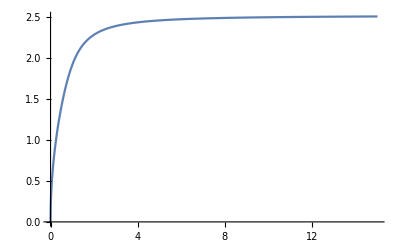

```mathematica
Plot[2 √x Hypergeometric2F1[1/8,1/2,9/8,-x^4],{x,0,15},AxesOrigin->{0,0}]
```

```mathematica
u[x_,y_]:=x/(1+√(x^2+y^2))+I y/(1+√(x^2+y^2))
```

```mathematica
u[0,0]
u[1,0]
u[-1/10,0]
u[0,1]
u[0,10000]
u[4,40000]//N
```

0

1/2

-1/11

ⅈ/2

(10000 ⅈ)/10001

0.0000999975+0.999975 ⅈ

```mathematica
f[n_]:=1/6 n(n+1)(2n+1)
```

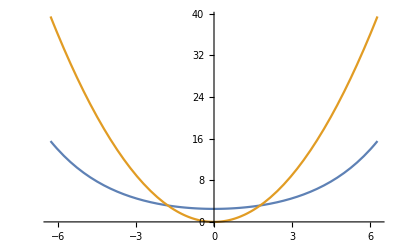

```mathematica
Plot[{1/(.4)Cosh[.4x],x^2},{x,-2π,2π},AxesOrigin->{0,0}]
```

```mathematica
g[x_]:=1/(.4)Cosh[.4x]
g[4]
```

6.44366

```mathematica
D[Sin[2 x],{x,2}]
```

-4 Sin[2 x]

```mathematica
Sum[Binomial[2 n,n]/5^n,{n,0,Infinity}]
```

√5

```mathematica
ClearAll[t]
√5//N
t[n_]:=Sum[Binomial[2 k,k]/5^k,{k,0,n}]
Table[{x,t[x],N[t[x],30]},{x,300,300,1}]//tf
```

2.23607

300 | 1097706669630572144894545496943760474358880269698902446207288050214602877896225576790278986395677818997032568135799036724199158642635176643121554041554132538712900686235904960903870751064403907678589373307857531/490909346529772655309577195498627564297521551249944956511154911718710525472171585646009788403733195227718357156513187851316791861042471890280751482410896345225310546445986192853894181098439730703830718994140625 | 2.23606797749978969640917366873

```mathematica
N[√5,20]
N[27830170372634509880870279963549505484935735667240385312343015249203154001996569094159690935670620348157706568501697494703673680727230238449/12446030555722283414288128107560248481180504337442334266202233229579397668070766882367889646251427233913933179110244964249432086944580078125,20]
```

2.2360679774997896964

2.2360679774997896964

```mathematica
m:={{1,-1,1},{1,-1,-1},{0,0,1}}
m:={{2x,-y,z},{x,-2y,+4z},{0,0,a}}
LinearSolve[m,{1,12,1}]
```

{-(2 (5 a-z))/(3 a x),(-23 a+7 z)/(3 a y),1/a}

```mathematica
LinearSolve[m,{1,0}]
```

{2/(3 x),1/(3 y),0}

```mathematica
Subsets[Sort[{2/(3 x),1/(3 y),0}]]
```

{{},{0},{2/(3 x)},{1/(3 y)},{0,2/(3 x)},{0,1/(3 y)},{2/(3 x),1/(3 y)},{0,2/(3 x),1/(3 y)}}

```mathematica
Eigenvalues[{{2,6},{0,-1}}]
Eigenvectors[{{2,6},{0,-1}}]
```

{2,-1}

{{1,0},{-2,1}}

```mathematica
Sin[π/2]
```

1

```mathematica
s:=Sphere[{0,0,0},2.5]
c:=Cylinder[{{0,0,-1},{0,0,1}},2.5]
RegionPlot3D[c,PlotPoints->40,PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
?VectorPlot
```

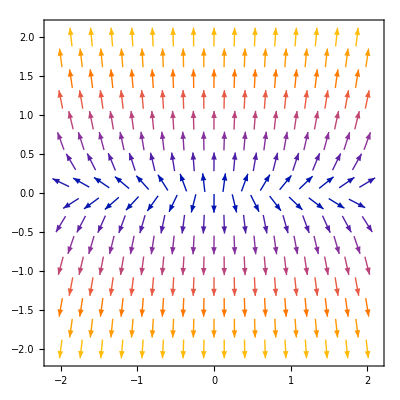

```mathematica
VectorPlot[Evaluate[D[x^2+8 y^2+1/8 x y,{{x,y}}]],{x,-2,2},{y,-2,2}]
```

```mathematica
UnitDimensions["Coulombs"]
```

{{ElectricCurrentUnit,1},{TimeUnit,1}}

```mathematica
FormulaData[]//tf
```

AbbeNumberHelium |  |  |  |  | 
AbbeNumberHydrogen |  |  |  |  | 
AbbeNumberMercury |  |  |  |  | 
AcceleratingFrequency |  |  |  |  | 
AccelerationNumber |  |  |  |  | 
AdiabaticProcess |  |  |  |  | 
Albedo |  |  |  |  | 
AlfvenNumber |  |  |  |  | 
AngleSubtended |  |  |  |  | 
AngularDiameter |  |  |  |  | 
AngularFrequency |  |  |  |  | 
AnnulusAreaMomentOfInertia |  |  |  |  | 
AntiKnockIndex |  |  |  |  | 
ApparentMagnitudeIntensity |  |  |  |  | 
ArchimedesNumber |  |  |  |  | 
ArrheniusNumber |  |  |  |  | 
AtkinsonCycle |  |  |  |  | 
AtwoodNumber |  |  |  |  | 
AvogadrosLaw |  |  |  |  | 
AxialMemberDeformation |  |  |  |  | 
BagnoldNumber |  |  |  |  | 
BagnoldNumberForSolidParticles |  |  |  |  | 
BaseballBattingAverage |  |  |  |  | 
BaseballGameScore |  |  |  |  | 
BaseballIsolatedPower |  |  |  |  | 
BaseballOnBasePercentagePlusSluggingPercentage |  |  |  |  | 
BaseballPythagoreanWinExpectancy |  |  |  |  | 
BaseballRangeFactor |  |  |  |  | 
BaseballSluggingPercentage |  |  |  |  | 
BasketballAssistRate |  |  |  |  | 
BasketballEffectiveFieldGoalPercentage |  |  |  |  | 
BasketballFieldGoalPercentage |  |  |  |  | 
BasketballTrueShootingPercentage |  |  |  |  | 
BasketballUsageRate |  |  |  |  | 
BealeNumber |  |  |  |  | 
BejanNumberHeatTransfer |  |  |  |  | 
BellColemanCycle |  |  |  |  | 
BernoullisEquation |  |  |  |  | 
BetheFormula |  |  |  |  | 
BimetallicStrip |  |  |  |  | 
BinghamCompressionNumber |  |  |  |  | 
BiotNumberHeatTransfer |  |  |  |  | 
BirthdayProblemApproximation |  |  |  |  | 
BlackHoleHawkingRadiationPower |  |  |  |  | 
BlackHoleLifetime |  |  |  |  | 
BlasiusBoundaryLayerThickness |  |  |  |  | 
BlasiusDisplacementThickness |  |  |  |  | 
BlasiusSkinFriction |  |  |  |  | 
BloodOxygen |  |  |  |  | 
BodyMassIndex |  |  |  |  | 
BondNumber |  |  |  |  | 
BoseEinsteinDistribution |  |  |  |  | 
BouguerAnomaly |  |  |  |  | 
BoussinesqNumber |  |  |  |  | 
BoyleNumber |  |  |  |  | 
BoylesLaw |  |  |  |  | 
BrakingTorque |  |  |  |  | 
BraytonCycle |  |  |  |  | 
BrewsterAngle |  |  |  |  | 
BrinellHardness |  |  |  |  | 
BrinkmanNumber |  |  |  |  | 
BrinkmanRheologicalNumber |  |  |  |  | 
BulkConcentration |  |  |  |  | 
Buoyancy |  |  |  |  | 
BurpeeRepetitions |  |  |  |  | 
CableCapacitance |  |  |  |  | 
Capacitance |  |  |  |  | 
CapacitanceParallel |  |  |  |  | 
CapacitanceSeries |  |  |  |  | 
CapillaryAction |  |  |  |  | 
CapillaryNumber |  |  |  |  | 
CapitalAssetPricingModel |  |  |  |  | 
CapitalRecoveryFactor |  |  |  |  | 
CardiacOutput |  |  |  |  | 
CartesianToPolar |  |  |  |  | 
CatheterFlowRate |  |  |  |  | 
CauchyNumber |  |  |  |  | 
CentrifugalPump |  |  |  |  | 
CerenkovRadiation |  |  |  |  | 
ChandrasekharNumber |  |  |  |  | 
ChargedBall |  |  |  |  | 
ChargedSphere |  |  |  |  | 
CharlesLaw |  |  |  |  | 
CircleArcLength |  |  |  |  | 
CircleArea |  |  |  |  | 
CircleAreaDiameter |  |  |  |  | 
CircleSectorArea |  |  |  |  | 
CircularCoilMaximalMagneticInduction |  |  |  |  | 
CircumferenceForm1 |  |  |  |  | 
CircumferenceForm2 |  |  |  |  | 
CloudBaseHeight |  |  |  |  | 
CoaxialCableSelfInductance |  |  |  |  | 
CohensD |  |  |  |  | 
CombinedGasLaw |  |  |  |  | 
CommodityContractsOptimalNumber |  |  |  |  | 
ComplementProbability |  |  |  |  | 
CompoundAnnualGrowthRate |  |  |  |  | 
ComptonWavelength |  |  |  |  | 
ConcentrationConversion |  |  |  |  | 
ConeMomentOfInertia |  |  |  |  | 
ContinuousCapitalRecoveryFactor |  |  |  |  | 
CoulombsLaw |  |  |  |  | 
CowlingMagneticNumber |  |  |  |  | 
CowlingNumber1 |  |  |  |  | 
CrunchRepetitions |  |  |  |  | 
CuboidMomentOfInertia |  |  |  |  | 
CyclotronFrequency |  |  |  |  | 
CylinderMomentOfInertia |  |  |  |  | 
DeanNumber |  |  |  |  | 
DecibelToRatio |  |  |  |  | 
DepthOfField |  |  |  |  | 
DieselCycle |  |  |  |  | 
DifferentialAmplifier |  |  |  |  | 
DifferentialGearRatio |  |  |  |  | 
DilutionEquation |  |  |  |  | 
DiskMomentOfInertia |  |  |  |  | 
DittusBoelterEquation |  |  |  |  | 
DividendDiscountModel |  |  |  |  | 
DolbearsLaw |  |  |  |  | 
DopplerBlueshift |  |  |  |  | 
DopplerRedshift |  |  |  |  | 
DoyleLogRule |  |  |  |  | 
DragCoefficient |  |  |  |  | 
DrakeEquation |  |  |  |  | 
DrivingDistanceSpeedTime |  |  |  |  | 
DurationBasedHedgeRatio |  |  |  |  | 
DynamicCapillaryNumber |  |  |  |  | 
EarthCircularOrbitPeriod |  |  |  |  | 
EarthquakeDowndipRuptureWidth |  |  |  |  | 
EarthquakeFaultSlip |  |  |  |  | 
EarthquakeFaultSlipRate |  |  |  |  | 
EarthquakeRuptureArea |  |  |  |  | 
EarthquakeRuptureLength |  |  |  |  | 
EckertNumber |  |  |  |  | 
EconomicValueAdded |  |  |  |  | 
EkmanNumber |  |  |  |  | 
ElasticCollision |  |  |  |  | 
ElectricalEnergy |  |  |  |  | 
EllipseArea |  |  |  |  | 
EllipseEccentricity |  |  |  |  | 
EllipsoidVolume |  |  |  |  | 
EllipticalLaminaMomentOfInertia |  |  |  |  | 
EllipticOrbitFormula |  |  |  |  | 
EnergyEfficiency |  |  |  |  | 
EotvosNumber |  |  |  |  | 
EquivalentSoundLevel |  |  |  |  | 
EricssonCycle |  |  |  |  | 
ErlangB |  |  |  |  | 
ErlangC |  |  |  |  | 
EscapeVelocity |  |  |  |  | 
EulerCharacteristic |  |  |  |  | 
ExposureValue |  |  |  |  | 
FannoFlow |  |  |  |  | 
FieldOfView |  |  |  |  | 
FirstLawOfThermodynamics |  |  |  |  | 
FirstOrderArrheniusEquation |  |  |  |  | 
FluidColumnPressure |  |  |  |  | 
FNumber |  |  |  |  | 
FNumberArithmetic |  |  |  |  | 
FootballPasserRating |  |  |  |  | 
ForceComponents |  |  |  |  | 
FourierNumberMassTransfer |  |  |  |  | 
FouriersLaw |  |  |  |  | 
FreeWaterDeficit |  |  |  |  | 
FrequencyPeriodRelation |  |  |  |  | 
FresnelNumber |  |  |  |  | 
FroudeNumber |  |  |  |  | 
GayLussacNumber |  |  |  |  | 
GayLussacsLaw |  |  |  |  | 
GlassDelta |  |  |  |  | 
GoldenRatio |  |  |  |  | 
GraetzNumberHeatTransfer |  |  |  |  | 
GrashofNumber |  |  |  |  | 
GravitationalPotentialEnergy |  |  |  |  | 
GravitationalRedshift |  |  |  |  | 
GrossDomesticProductExpenditures |  |  |  |  | 
GrossDomesticProductIncome |  |  |  |  | 
GrossDomesticProductValueAdded |  |  |  |  | 
HalfDiskAreaMomentOfInertia |  |  |  |  | 
HamCookingTime |  |  |  |  | 
HartmannNumber |  |  |  |  | 
HazenWilliamsEquation |  |  |  |  | 
HeatEngineEfficiency |  |  |  |  | 
HedgeEffectiveness |  |  |  |  | 
HelmholtzResonatorFrequency |  |  |  |  | 
HexagonAreaMomentOfInertia |  |  |  |  | 
HohmannAngularAlignment |  |  |  |  | 
HollowCylinderMechanicalStress |  |  |  |  | 
HydraulicConductivity |  |  |  |  | 
HyperfocalDistance |  |  |  |  | 
HypsometricEquation |  |  |  |  | 
IdealDilutionEquation |  |  |  |  | 
IdealSolenoidMagneticInduction |  |  |  |  | 
IlluminanceFromLuminousIntensity |  |  |  |  | 
Impulse |  |  |  |  | 
InclinedSpanSag |  |  |  |  | 
IndicatedHorsepower |  |  |  |  | 
InductiveReactance |  |  |  |  | 
InfinitelyLongWire |  |  |  |  | 
InstrumentationAmplifier |  |  |  |  | 
InternationalQuarterInchLogRule |  |  |  |  | 
IntrinsicPermeability |  |  |  |  | 
InvertingAmplifier |  |  |  |  | 
IsobaricProcess |  |  |  |  | 
IsochoricProcess |  |  |  |  | 
IsothermalProcess |  |  |  |  | 
IVInfusionRate |  |  |  |  | 
JohnsonNyquistNoisePowerSpectralDensity |  |  |  |  | 
JohnsonNyquistNoiseVoltage |  |  |  |  | 
JumpingJackRepetitions |  |  |  |  | 
KeplersFirstLaw |  |  |  |  | 
KineticEnergy |  |  |  |  | 
KineticEnergyRelativistic |  |  |  |  | 
KineticFrictionCoefficient |  |  |  |  | 
KnoopHardness |  |  |  |  | 
KnudsenNumber |  |  |  |  | 
LaplaceNumber |  |  |  |  | 
LarmorPower |  |  |  |  | 
LawOfCosines |  |  |  |  | 
LawOfHaversines |  |  |  |  | 
LawOfSines |  |  |  |  | 
LawOfTangents |  |  |  |  | 
LengthContractionRelativistic |  |  |  |  | 
LenoirCycle |  |  |  |  | 
LevelSpanSag |  |  |  |  | 
LeverMechanicalAdvantage |  |  |  |  | 
LiftCoefficient |  |  |  |  | 
LightAberrationRelativistic |  |  |  |  | 
LineSlope |  |  |  |  | 
LogOddsRatio |  |  |  |  | 
LorentzFactor |  |  |  |  | 
LorentzNumber |  |  |  |  | 
LuminosityAbsoluteMagnitude |  |  |  |  | 
LuminosityApparentMagnitudeDistance |  |  |  |  | 
LuminosityDistance |  |  |  |  | 
LuminosityEnergy |  |  |  |  | 
MachNumber |  |  |  |  | 
MagneticEnergyDensity |  |  |  |  | 
ManningFormula |  |  |  |  | 
MassDensity |  |  |  |  | 
MassLuminosityRelationship |  |  |  |  | 
MechanicalStress |  |  |  |  | 
MelScale |  |  |  |  | 
MinimumPowerRequiredToMoveObject |  |  |  |  | 
MinimumVarianceHedgeRatio |  |  |  |  | 
MirrorEquationsConcave |  |  |  |  | 
MirrorEquationsConvex |  |  |  |  | 
ModifiedInternalRateOfReturn |  |  |  |  | 
ModulusRelation |  |  |  |  | 
MohrCoulombFailureCriterion |  |  |  |  | 
MolarityDensityConversion |  |  |  |  | 
MomentOfInertiaRatio |  |  |  |  | 
MonoproticStrongAcidBaseTitration |  |  |  |  | 
MorseEquation |  |  |  |  | 
MultipleLens |  |  |  |  | 
NegativePredictiveValue |  |  |  |  | 
NewtonsLawOfCooling |  |  |  |  | 
NewtonsLawOfUniversalGravitation |  |  |  |  | 
NewtonsSecondLawConstantMass |  |  |  |  | 
NominalToEffectiveInterestRate |  |  |  |  | 
NominalToEffectiveInterestRateContinuous |  |  |  |  | 
NoninvertingAmplifier |  |  |  |  | 
NormalizedFrequency |  |  |  |  | 
NozzlePressureDrop |  |  |  |  | 
NusseltNumberHeatTransfer |  |  |  |  | 
OddsRatio |  |  |  |  | 
OhmsLaw |  |  |  |  | 
OpticalPower |  |  |  |  | 
OttoCycle |  |  |  |  | 
OxygenIndex |  |  |  |  | 
PageSpeed |  |  |  |  | 
PantoscopicTilt |  |  |  |  | 
ParallaxDistance |  |  |  |  | 
ParallelAxisTheorem |  |  |  |  | 
ParallelResistorCapacitorCircuit |  |  |  |  | 
ParallelResistorInductorCapacitorCircuit |  |  |  |  | 
ParallelResistorInductorCircuit |  |  |  |  | 
ParallelWiresSelfInductance |  |  |  |  | 
PaschensLaw |  |  |  |  | 
PecletNumberMassTransfer |  |  |  |  | 
PentagonAreaMomentOfInertia |  |  |  |  | 
PlantAllometryTrunkDiameterHeight |  |  |  |  | 
pOH |  |  |  |  | 
PointCharge |  |  |  |  | 
PointMassMomentOfInertia |  |  |  |  | 
PoissonRatio |  |  |  |  | 
PolarToCartesian |  |  |  |  | 
PolytropicProcess |  |  |  |  | 
PooledStandardDeviation |  |  |  |  | 
PooledVariance |  |  |  |  | 
PopulationGrowth |  |  |  |  | 
PositivePredictiveValue |  |  |  |  | 
PowerResistanceCurrent |  |  |  |  | 
PowerResistanceVoltage |  |  |  |  | 
PowerVoltageCurrent |  |  |  |  | 
PresentValueFutureValueContinuous |  |  |  |  | 
PresentValueFutureValueContinuousDates |  |  |  |  | 
Pressure |  |  |  |  | 
Prevalence |  |  |  |  | 
PrincipalStress |  |  |  |  | 
PrismRefraction |  |  |  |  | 
ProbabilityOfExceedance |  |  |  |  | 
Projectile |  |  |  |  | 
ProjectileSlantRange |  |  |  |  | 
PulleySystemMechanicalAdvantage |  |  |  |  | 
PullUpRepetitions |  |  |  |  | 
PushUpRepetitions |  |  |  |  | 
PythagoreanTheorem |  |  |  |  | 
QuadraticEquation |  |  |  |  | 
QuarterDiskAreaMomentOfInertia |  |  |  |  | 
RadioHorizonDistance |  |  |  |  | 
RainbowAltitude |  |  |  |  | 
RangeToAircraft |  |  |  |  | 
RankineCycle |  |  |  |  | 
Rapidity |  |  |  |  | 
RayleighFlow |  |  |  |  | 
RealRateOfReturn |  |  |  |  | 
RectangleArea |  |  |  |  | 
RectangleAreaMomentOfInertia |  |  |  |  | 
RedlichKwongEquation |  |  |  |  | 
RedshiftRelativistic |  |  |  |  | 
ReducedMass |  |  |  |  | 
RefractiveIndex |  |  |  |  | 
RegularNGonArea |  |  |  |  | 
RelativeGrahamValue |  |  |  |  | 
RenalFailureIndex |  |  |  |  | 
Resistance |  |  |  |  | 
ResistanceParallel |  |  |  |  | 
ResistanceSeries |  |  |  |  | 
Resistivity |  |  |  |  | 
RespiratoryQuotient |  |  |  |  | 
ReynoldsMagneticNumber |  |  |  |  | 
RichardsonNumber |  |  |  |  | 
RichterScaleMagnitudeDefinition |  |  |  |  | 
RichterScaleMagnitudeToEnergy |  |  |  |  | 
RightTriangleSides |  |  |  |  | 
RigidBodyAngularMomentum |  |  |  |  | 
RocketEquation |  |  |  |  | 
Rolling |  |  |  |  | 
RollingFrictionCoefficient |  |  |  |  | 
RollingResistanceCoefficient |  |  |  |  | 
RoomArea |  |  |  |  | 
RoomAreaUnits |  |  |  |  | 
RossbyNumber |  |  |  |  | 
RotationalKineticEnergy |  |  |  |  | 
RotationalPower |  |  |  |  | 
RuleOfSeventy |  |  |  |  | 
RunningInTheRain |  |  |  |  | 
RydbergFormula |  |  |  |  | 
SalaryCalculation |  |  |  |  | 
SampleSizeForPopulationMean |  |  |  |  | 
SandCastleStability |  |  |  |  | 
ScribnerLogRule |  |  |  |  | 
SeagerEquation |  |  |  |  | 
SecondOrderArrheniusEquation |  |  |  |  | 
SeismicMomentMagnitudeToEnergy |  |  |  |  | 
Sensitivity |  |  |  |  | 
SeriesResistorCapacitorCircuit |  |  |  |  | 
SeriesResistorInductorCapacitorCircuit |  |  |  |  | 
SeriesResistorInductorCircuit |  |  |  |  | 
SerumOsmolarity |  |  |  |  | 
SIModel |  |  |  |  | 
SimpleInterest |  |  |  |  | 
SingleLayerCircularCoilSelfInductance |  |  |  |  | 
SingleLayerCircularCoilSmallRadiusSelfInductance |  |  |  |  | 
SingleLayerRectangularCoilSelfInductance |  |  |  |  | 
SitUpRepetitions |  |  |  |  | 
SodiumDeficit |  |  |  |  | 
SolidEllipsoidMomentOfInertia |  |  |  |  | 
Specificity |  |  |  |  | 
SpectralLineNaturalBroadening |  |  |  |  | 
SphereMomentOfInertia |  |  |  |  | 
SphericalLawOfSines |  |  |  |  | 
SphericalLawOfTangents |  |  |  |  | 
SpheroidVolume |  |  |  |  | 
SpringConstant |  |  |  |  | 
SpringMaximumForce |  |  |  |  | 
SpringMaximumShearStress |  |  |  |  | 
StantonNumber |  |  |  |  | 
StefanBoltzmannLaw |  |  |  |  | 
StockContractsOptimalNumber |  |  |  |  | 
StokesFlow |  |  |  |  | 
StrehlRatio |  |  |  |  | 
StringWavePropagation |  |  |  |  | 
StrouhalNumber |  |  |  |  | 
SubjectMagnification |  |  |  |  | 
SutherlandFormula |  |  |  |  | 
SwellingInterfaceNumber |  |  |  |  | 
SynchronousSpeed |  |  |  |  | 
TelescopeLightGatheringPower |  |  |  |  | 
TelescopeMagnifyingPower |  |  |  |  | 
ThermalDeformation |  |  |  |  | 
ThermalSpeed |  |  |  |  | 
ThermodynamicEnergy |  |  |  |  | 
ThinFilmInterferenceConstructive |  |  |  |  | 
ThinFilmInterferenceDestructive |  |  |  |  | 
ThinLensEquation |  |  |  |  | 
ThinRodMomentOfInertia |  |  |  |  | 
ThrowingAngle |  |  |  |  | 
TimeDilationRelativistic |  |  |  |  | 
TorricellisTheorem |  |  |  |  | 
Torsion |  |  |  |  | 
TorusVolume |  |  |  |  | 
TotalInternalReflection |  |  |  |  | 
TranstubularPotassiumGradient |  |  |  |  | 
TrapezoidArea |  |  |  |  | 
TrapezoidAreaMomentOfInertia |  |  |  |  | 
TriangleAreaBH |  |  |  |  | 
TriangleAreaMomentOfInertia |  |  |  |  | 
TriangleAreaSSS |  |  |  |  | 
TriangularPlateMomentOfInertia |  |  |  |  | 
TurkeyCookingTime |  |  |  |  | 
TurkeyFryingTime |  |  |  |  | 
TurkeySmokingTime |  |  |  |  | 
TwoInfinitelyLongParallelWires |  |  |  |  | 
TwoUnionProbability |  |  |  |  | 
UniformDensitySphereGravitationalBindingEnergy |  |  |  |  | 
VanDerWaalsEquation |  |  |  |  | 
VantHoffEquation |  |  |  |  | 
VantHoffFactor |  |  |  |  | 
VectorProjection |  |  |  |  | 
VelocityAdditionRelativistic |  |  |  |  | 
VelocityComponents |  |  |  |  | 
VickersHardness |  |  |  |  | 
Viscosity |  |  |  |  | 
WaterHammerFast |  |  |  |  | 
WaterHammerSlow |  |  |  |  | 
WaterWavePhaseSpeed |  |  |  |  | 
Wavenumber |  |  |  |  | 
WeberNumber |  |  |  |  | 
WeightedAverageCostOfCapital |  |  |  |  | 
WheelAndAxleMechanicalAdvantage |  |  |  |  | 
WindTurbine |  |  |  |  | 
WordSpeed |  |  |  |  | 
YoungsModulus |  |  |  |  | 
ZeissFormula |  |  |  |  | 
ZernikeOpticalAberration |  |  |  |  | 
AngleOfView | Height |  |  |  | 
AngleOfView | Width |  |  |  | 
Annuity | FutureValue |  |  |  | 
Annuity | PresentValue |  |  |  | 
AnnuityDue | FutureValue |  |  |  | 
AnnuityDue | PresentValue |  |  |  | 
AverageAngularVelocity | Angles |  |  |  | 
AverageAngularVelocity | AngularDisplacement |  |  |  | 
AverageAngularVelocity | Velocities |  |  |  | 
AverageSpeed | Positions |  |  |  | 
AverageSpeed | Speeds |  |  |  | 
AverageSpeed | TotalDistance |  |  |  | 
BarometricFormula | MassDensity |  |  |  | 
BarometricFormula | Pressure |  |  |  | 
BaseballBattingAverageOnBallsInPlay | SacrificeFlies |  |  |  | 
BaseballBattingAverageOnBallsInPlay | Standard |  |  |  | 
BaseballBattingAverageOnBallsInPlay | Strikeouts |  |  |  | 
BaseballEarnedRunAverage | Outs |  |  |  | 
BaseballEarnedRunAverage | Standard |  |  |  | 
BaseballFieldingIndependentPitching | ExpectedHomeruns |  |  |  | 
BaseballFieldingIndependentPitching | Homeruns |  |  |  | 
BaseballOnBasePercentage | HitByPitch |  |  |  | 
BaseballOnBasePercentage | SacrificeFlies |  |  |  | 
BaseballOnBasePercentage | Standard |  |  |  | 
BaseballRunsCreated | Standard |  |  |  | 
BaseballSecondaryAverage | CaughtStealing |  |  |  | 
BaseballSecondaryAverage | Standard |  |  |  | 
BaseballSecondaryAverage | StolenBases |  |  |  | 
BaseballWalksPlusHitsPerInning | Outs |  |  |  | 
BaseballWalksPlusHitsPerInning | Standard |  |  |  | 
BaseballWeightedOnBaseAverage | HitByPitch |  |  |  | 
BaseballWeightedOnBaseAverage | ReachedBaseOnError |  |  |  | 
BaseballWeightedOnBaseAverage | Standard |  |  |  | 
BeerLambertLaw | DecadicAbsorbance |  |  |  | 
BeerLambertLaw | NapierianAbsorbance |  |  |  | 
BenchStepping | StepCount |  |  |  | 
BenchStepping | StepHeight |  |  |  | 
BenchStepping | StepRate |  |  |  | 
BenjaminGrahamFormula | CurrentYieldAAACorporateBonds |  |  |  | 
BenjaminGrahamFormula | Standard |  |  |  | 
Bicycling | Pace |  |  |  | 
Bicycling | Speed |  |  |  | 
BlackbodyLuminosity | Diameter |  |  |  | 
BlackbodyLuminosity | Radius |  |  |  | 
BlackHoleEntropy | AngularMomentum |  |  |  | 
BlackHoleEntropy | Charge |  |  |  | 
BlackHoleEntropy | Standard |  |  |  | 
BlackHoleEventHorizonArea | AngularMomentum |  |  |  | 
BlackHoleEventHorizonArea | Charge |  |  |  | 
BlackHoleEventHorizonArea | Standard |  |  |  | 
BlackHoleEventHorizonRadius | AngularMomentum |  |  |  | 
BlackHoleEventHorizonRadius | Charge |  |  |  | 
BlackHoleEventHorizonRadius | Standard |  |  |  | 
BlackHoleSurfaceGravity | AngularMomentum |  |  |  | 
BlackHoleSurfaceGravity | Charge |  |  |  | 
BlackHoleSurfaceGravity | Standard |  |  |  | 
BlackHoleTemperature | AngularMomentum |  |  |  | 
BlackHoleTemperature | Charge |  |  |  | 
BlackHoleTemperature | Standard |  |  |  | 
BloodGlucose | MeanPlasmaGlucose |  |  |  | 
BloodGlucose | MeanPlasmaGlucoseMolarity |  |  |  | 
BodensteinNumber | ThermalConductivity |  |  |  | 
BodensteinNumber | ThermalDiffusivity |  |  |  | 
BoilingPointElevation | SolventProperties |  |  |  | 
BoilingPointElevation | Standard |  |  |  | 
BondDuration | MacaulayDuration |  |  |  | 
BondDuration | ModifiedDuration |  |  |  | 
BoseCondensationTemperature | NumberDensity |  |  |  | 
BoseCondensationTemperature | Pressure |  |  |  | 
BoseCondensationTemperature | Volume |  |  |  | 
BoussinesqApproximationParameter | ApproximatedAccelerationOfGravity |  |  |  | 
BoussinesqApproximationParameter | FluidDensities |  |  |  | 
BraggsLaw | Energy |  |  |  | 
BraggsLaw | Standard |  |  |  | 
BrownellKatzNumber | BondNumber |  |  |  | 
BrownellKatzNumber | Viscosity |  |  |  | 
BussardRamjet | MatterDrive |  |  |  | 
BussardRamjet | PhotonDrive |  |  |  | 
CapacitiveReactance | AngularFrequency |  |  |  | 
CapacitiveReactance | CircuitFrequency |  |  |  | 
CarnotCycle | HeatEngine |  |  |  | 
CarnotCycle | HeatPump |  |  |  | 
CarnotCycle | Refrigerator |  |  |  | 
CasimirEffect | Force |  |  |  | 
CasimirEffect | Pressure |  |  |  | 
CentripetalAcceleration | AngularVelocity |  |  |  | 
CentripetalAcceleration | RotationSpeed |  |  |  | 
CentripetalForce | AngularVelocity |  |  |  | 
CentripetalForce | RotationSpeed |  |  |  | 
CircleSectorArea | Angle |  |  |  | 
CircleSectorArea | ArcLength |  |  |  | 
CircularCurrentLoop | Distance |  |  |  | 
CircularCurrentLoop | Loops |  |  |  | 
CircularCurrentLoop | Standard |  |  |  | 
CircularOrbitInMagneticField | Momentum |  |  |  | 
CircularOrbitInMagneticField | Speed |  |  |  | 
CircularOrbitSpeed | Altitude |  |  |  | 
CircularOrbitSpeed | OrbitRadius |  |  |  | 
ColebrookWhiteEquation | DarcyFrictionFactor |  |  |  | 
ColebrookWhiteEquation | PipeRoughnessHeight |  |  |  | 
ComptonShift | Wavelengths |  |  |  | 
ComptonShift | WavelengthShift |  |  |  | 
CoriolisEffect | Force |  |  |  | 
CoriolisEffect | Standard |  |  |  | 
CorrectiveLensFarsighted | LensDiopter |  |  |  | 
CorrectiveLensFarsighted | OSDLensDiopter |  |  |  | 
CorrectiveLensShortsighted | LensDiopter |  |  |  | 
CorrectiveLensShortsighted | OSDLensDiopter |  |  |  | 
CriticalEulerBucklingForce | ColumnLength |  |  |  | 
CriticalEulerBucklingForce | EffectiveColumnLength |  |  |  | 
CriticalEulerBucklingForce | EffectiveColumnLengthFactor |  |  |  | 
CrossCountrySkiing | Pace |  |  |  | 
CrossCountrySkiing | Speed |  |  |  | 
CuboidVolumeDepth | Area |  |  |  | 
CuboidVolumeDepth | LengthDepth |  |  |  | 
CuboidVolumeWidth | Area |  |  |  | 
CuboidVolumeWidth | LengthWidth |  |  |  | 
CylinderMechanicalStress | Diameter |  |  |  | 
CylinderMechanicalStress | Radius |  |  |  | 
DarcysLaw | HydraulicGradient |  |  |  | 
DarcysLaw | PressureDifference |  |  |  | 
DataSpeed | DataRate |  |  |  | 
DataSpeed | DownstreamRate |  |  |  | 
DataSpeed | UpstreamRate |  |  |  | 
DeborahNumber | MixingTime |  |  |  | 
DeborahNumber | MolecularTimescale |  |  |  | 
DeborahNumber | RelaxationTimescale |  |  |  | 
DefrostingTime | Air |  |  |  | 
DefrostingTime | Water |  |  |  | 
DeLavalNozzle | HeatCapacities |  |  |  | 
DeLavalNozzle | HeatCapacityRatio |  |  |  | 
DiabetesDoseAdjustmentTravel | TimeZonesCrossedEast |  |  |  | 
DiabetesDoseAdjustmentTravel | TimeZonesCrossedWest |  |  |  | 
DieselCycle | CutoffRatio |  |  |  | 
DiffractionGrating | GratingIncidenceAngle |  |  |  | 
DiffractionGrating | Standard |  |  |  | 
DilutionEquation | Solution |  |  |  | 
DinosaurWalkingSpeed | FootLength |  |  |  | 
DinosaurWalkingSpeed | HipHeight |  |  |  | 
DiscountedSecurity | DayCountConvention |  |  |  | 
DiscountedSecurity | Standard |  |  |  | 
DiskAreaMomentOfInertia | Diameter |  |  |  | 
DiskAreaMomentOfInertia | Radius |  |  |  | 
DiskSelfCapacitance | ElectricPermittivity |  |  |  | 
DiskSelfCapacitance | RelativeElectricPermittivity |  |  |  | 
DiskSelfCapacitance | VacuumPermittivity |  |  |  | 
DistanceSpeedTime | Acceleration |  |  |  | 
DistanceSpeedTime | ConstantSpeed |  |  |  | 
DistanceSpeedTime | InitialPosition |  |  |  | 
DistanceSpeedTimeCircularForm | AngularAcceleration |  |  |  | 
DistanceSpeedTimeCircularForm | ConstantSpeed |  |  |  | 
DistanceSpeedTimeCircularForm | InitialAngle |  |  |  | 
DopplerBroadening | Frequency |  |  |  | 
DopplerBroadening | Wavelength |  |  |  | 
DopplerShift | Frequency |  |  |  | 
DopplerShift | Ratio |  |  |  | 
DopplerShiftRelativistic | Frequency |  |  |  | 
DopplerShiftRelativistic | Ratio |  |  |  | 
DopplerShiftRelativistic | Wavelength |  |  |  | 
ElasticCollision2D | Angle |  |  |  | 
ElasticCollision2D | Radius |  |  |  | 
ElectromagneticSkinDepth | AngularFrequency |  |  |  | 
ElectromagneticSkinDepth | Frequency |  |  |  | 
EllipticalMachine | Cadence |  |  |  | 
EllipticalMachine | Pace |  |  |  | 
EllipticalMachine | Speed |  |  |  | 
EllipticalMachine | StrideLength |  |  |  | 
EllipticCylinderVolume | Mass |  |  |  | 
EllipticCylinderVolume | Volume |  |  |  | 
EnergyRelativistic | MovingMass |  |  |  | 
EnergyRelativistic | RestMass |  |  |  | 
EngineeringStrain | LengthDifference |  |  |  | 
EngineeringStrain | Lengths |  |  |  | 
EquivalentDoseOfIonizingRadiation | IonizingRadiationType |  |  |  | 
EquivalentDoseOfIonizingRadiation | RadiationWeightingFactor |  |  |  | 
EulerNumber | FrictionForce |  |  |  | 
EulerNumber | PressureDifference |  |  |  | 
ExponentialDecay | HalfLife |  |  |  | 
ExponentialDecay | Lifetime |  |  |  | 
FabryPerotInterferometer | FinesseCoefficient |  |  |  | 
FabryPerotInterferometer | PlateReflectance |  |  |  | 
FermiDiracDistribution | ChemicalPotential |  |  |  | 
FermiDiracDistribution | ChemicalPotentialEnergy |  |  |  | 
FermiEnergy | NumberDensity |  |  |  | 
FermiEnergy | Volume |  |  |  | 
FlowDischargeRate | Area |  |  |  | 
FlowDischargeRate | Diameter |  |  |  | 
FlowDischargeRate | HeightWidth |  |  |  | 
FlowDischargeRate | Radius |  |  |  | 
FourierNumber | ThermalConductivity |  |  |  | 
FourierNumber | ThermalDiffusivity |  |  |  | 
FourierNumberHeatTransfer | ThermalConductivity |  |  |  | 
FourierNumberHeatTransfer | ThermalDiffusivity |  |  |  | 
FreezingPointDepression | SolventProperties |  |  |  | 
FreezingPointDepression | Standard |  |  |  | 
FresnelEquation | PPolarized |  |  |  | 
FresnelEquation | SPolarized |  |  |  | 
FuelCost | FuelConsumption |  |  |  | 
FuelCost | FuelEconomy |  |  |  | 
FuelUsed | Volume |  |  |  | 
GalileiNumber | CharacteristicLength |  |  |  | 
GalileiNumber | ReynoldsNumber |  |  |  | 
GamblingCalculator | AmericanOdds |  |  |  | 
GamblingCalculator | DecimalOdds |  |  |  | 
GamblingCalculator | FractionalOdds |  |  |  | 
GoffGratchEquation | Ice |  |  |  | 
GoffGratchEquation | Water |  |  |  | 
GradePercent | GradePercent |  |  |  | 
GradePercent | SlopeAngle |  |  |  | 
GrahamsLaw | Fluxes |  |  |  | 
GrahamsLaw | FluxRatio |  |  |  | 
GravitationalAcceleration | Radius |  |  |  | 
GyromagneticRatio | Electron |  |  |  | 
GyromagneticRatio | Generic |  |  |  | 
HarmonicOscillator | Damping |  |  |  | 
HarmonicOscillator | Driving |  |  |  | 
HarmonicOscillator | FrequencyPeriod |  |  |  | 
HarmonicOscillator | NoInfluences |  |  |  | 
HarmonicOscillator | Pendulum |  |  |  | 
HarmonicOscillator | Spring |  |  |  | 
HarmonicOscillator | Torsion |  |  |  | 
HeatCapacityRatio | DegreesOfFreedom |  |  |  | 
HeatCapacityRatio | HeatCapacities |  |  |  | 
HeatCapacityRatio | SpecificHeatCapacities |  |  |  | 
HeatTransferCoefficient | HeatTransferRate |  |  |  | 
HeatTransferCoefficient | HeatTransferred |  |  |  | 
HelmholtzCoil | Coils |  |  |  | 
HelmholtzCoil | Distance |  |  |  | 
HelmholtzCoil | Standard |  |  |  | 
HendersonHasselbalchEquation | AcidityConstant |  |  |  | 
HendersonHasselbalchEquation | LogAcidityConstant |  |  |  | 
HohmannEntranceDeltaV | GravitationalParameter |  |  |  | 
HohmannEntranceDeltaV | Mass |  |  |  | 
HohmannExitDeltaV | GravitationalParameter |  |  |  | 
HohmannExitDeltaV | Mass |  |  |  | 
HohmannTotalDeltaV | GravitationalParameter |  |  |  | 
HohmannTotalDeltaV | Mass |  |  |  | 
HookesLaw | Force |  |  |  | 
HookesLaw | PotentialEnergy |  |  |  | 
HorizonDistance | ArbitraryPlanet |  |  |  | 
HorizonDistance | Earth |  |  |  | 
HorizontalCylinderLateralSurfaceArea | Diameter |  |  |  | 
HorizontalCylinderLateralSurfaceArea | Radius |  |  |  | 
HorizontalCylinderTotalSurfaceArea | Diameter |  |  |  | 
HorizontalCylinderTotalSurfaceArea | Radius |  |  |  | 
HorizontalCylinderVolume | Diameter |  |  |  | 
HorizontalCylinderVolume | Radius |  |  |  | 
HydrostaticPressure | AtmosphericPressure |  |  |  | 
HydrostaticPressure | Standard |  |  |  | 
IdealGasHeatCapacity | BoltzmannConstant |  |  |  | 
IdealGasHeatCapacity | MolarGasConstant |  |  |  | 
IdealGasInternalEnergy | BoltzmannConstant |  |  |  | 
IdealGasInternalEnergy | MolarGasConstant |  |  |  | 
IdealGasLaw | Density |  |  |  | 
IdealGasLaw | Volume |  |  |  | 
IdealGasSpeedOfSoundPressure | Density |  |  |  | 
IdealGasSpeedOfSoundPressure | SpecificGravity |  |  |  | 
IdealGasSpeedOfSoundTemperature | BoltzmannConstant |  |  |  | 
IdealGasSpeedOfSoundTemperature | MolarGasConstant |  |  |  | 
IdealTransformer | Current |  |  |  | 
IdealTransformer | Voltage |  |  |  | 
InclinedPlaneMechanicalAdvantage | LengthHeight |  |  |  | 
InclinedPlaneMechanicalAdvantage | Slope |  |  |  | 
InterestAtMaturitySecurity | DayCountConvention |  |  |  | 
InterestAtMaturitySecurity | Standard |  |  |  | 
JeansLength | SoundSpeed |  |  |  | 
JeansMass | SoundSpeed |  |  |  | 
JoulesLaw | ElectricCurrent |  |  |  | 
JoulesLaw | ElectricPotential |  |  |  | 
KeplersThirdLaw | Masses |  |  |  | 
KeplersThirdLaw | SingleMass |  |  |  | 
KeplersThirdLaw | Sun |  |  |  | 
KineticEnergySphere | Diameter |  |  |  | 
KineticEnergySphere | Radius |  |  |  | 
KineticEnergySphereRelativistic | Diameter |  |  |  | 
KineticEnergySphereRelativistic | Radius |  |  |  | 
LarmorFrequency | ParticleProperties |  |  |  | 
LarmorFrequency | Standard |  |  |  | 
LensMakerEquation | AmbientMediumRefractiveIndex |  |  |  | 
LensMakerEquation | Standard |  |  |  | 
LewisNumber | ThermalConductivity |  |  |  | 
LewisNumber | ThermalDiffusivity |  |  |  | 
LorentzForce | Current |  |  |  | 
LorentzForce | ParticleSpeed |  |  |  | 
MohrsCircle | PlaneNormalStrainX |  |  |  | 
MohrsCircle | PlaneNormalStrainY |  |  |  | 
MohrsCircle | PlaneNormalStressX |  |  |  | 
MohrsCircle | PlaneNormalStressY |  |  |  | 
MohrsCircle | PlaneShearStrain |  |  |  | 
MohrsCircle | PlaneShearStress |  |  |  | 
Momentum | KineticEnergy |  |  |  | 
Momentum | Speed |  |  |  | 
MomentumRelativistic | KineticEnergy |  |  |  | 
MomentumRelativistic | Velocity |  |  |  | 
MooresLaw | YearsFromNow |  |  |  | 
MultipleLensInContact | FourLenses |  |  |  | 
MultipleLensInContact | ThreeLenses |  |  |  | 
MultipleLensInContact | TwoLenses |  |  |  | 
MultipleSlitDiffraction | Wavelength |  |  |  | 
MultipleSlitDiffraction | Wavenumber |  |  |  | 
MythOfTheNines | Annually |  |  |  | 
MythOfTheNines | Monthly |  |  |  | 
MythOfTheNines | Weekly |  |  |  | 
NernstEquation | EquilibriumConstant |  |  |  | 
NernstEquation | ReactionQuotient |  |  |  | 
NumericalAperture | ApertureDiameter |  |  |  | 
NumericalAperture | FNumber |  |  |  | 
OscillationEnergy | Phase |  |  |  | 
OscillationEnergy | Standard |  |  |  | 
OxygenDelivery | CardiacOutput |  |  |  | 
OxygenDelivery | HeartRate |  |  |  | 
ParallelPlateCapacitance | ElectricPermittivity |  |  |  | 
ParallelPlateCapacitance | RelativeElectricPermittivity |  |  |  | 
ParallelPlateCapacitance | VacuumPermittivity |  |  |  | 
ParticleCollision | Inelastic |  |  |  | 
ParticleCollision | Surface |  |  |  | 
PecletNumber | ThermalConductivity |  |  |  | 
PecletNumber | ThermalDiffusivity |  |  |  | 
Pendulum | MomentOfInertia |  |  |  | 
Pendulum | Standard |  |  |  | 
PendulumSmallOscillations | MomentOfInertia |  |  |  | 
PendulumSmallOscillations | Standard |  |  |  | 
Perpetuity | AnnualPaymentGrowthRate |  |  |  | 
Perpetuity | Standard |  |  |  | 
pH | HPlusConcentration |  |  |  | 
pH | pOH |  |  |  | 
PhotonEnergy | AngularFrequency |  |  |  | 
PhotonEnergy | Frequency |  |  |  | 
PhotonEnergy | Wavelength |  |  |  | 
PhotonMomentum | Frequency |  |  |  | 
PhotonMomentum | SpectroscopicWavenumber |  |  |  | 
PhotonMomentum | Wavelength |  |  |  | 
PhotonWavelength | Energy |  |  |  | 
PhotonWavelength | Frequency |  |  |  | 
PhotonWavelength | Wavenumber |  |  |  | 
PhysicalActivityEnergyExpenditure | Female |  |  |  | 
PhysicalActivityEnergyExpenditure | Male |  |  |  | 
PixelConverter | PixelDensity |  |  |  | 
PixelConverter | StandardPixelDensity |  |  |  | 
pKa | AcidityConstant |  |  |  | 
pKa | Concentrations |  |  |  | 
PlanckRadiationLaw | Frequency |  |  |  | 
PlanckRadiationLaw | Wavelength |  |  |  | 
PoiseuillesLaw | Diameter |  |  |  | 
PoiseuillesLaw | Radius |  |  |  | 
PowerFactor | ElectricApparentPower |  |  |  | 
PrandtlNumber | ThermalConductivity |  |  |  | 
PrandtlNumber | ThermalDiffusivity |  |  |  | 
PresentValueFutureValue | CompoundingFrequencyDiscrete |  |  |  | 
PresentValueFutureValue | Standard |  |  |  | 
PresentValueFutureValueDates | CompoundingFrequencyDiscrete |  |  |  | 
PresentValueFutureValueDates | Standard |  |  |  | 
ProperVelocity | Rapidity |  |  |  | 
ProperVelocity | Velocity |  |  |  | 
QTCorrection | HeartRate |  |  |  | 
QTCorrection | RRInterval |  |  |  | 
RadiocarbonYears | RadiocarbonAmounts |  |  |  | 
RadiocarbonYears | SampleC14Ratio |  |  |  | 
RAIDArray | SpareDisks |  |  |  | 
RAIDArray | Standard |  |  |  | 
RaoultsLaw | PartialPressures |  |  |  | 
RaoultsLaw | VaporPressures |  |  |  | 
RayleighNumber | ThermalConductivity |  |  |  | 
RayleighNumber | ThermalDiffusivity |  |  |  | 
RayleighScatteringParticles | Diameter |  |  |  | 
RayleighScatteringParticles | Radius |  |  |  | 
RedshiftWavelength | Frequency |  |  |  | 
RedshiftWavelength | Wavelength |  |  |  | 
ResonantCavity | Conductivity |  |  |  | 
ResonantCavity | Resistivity |  |  |  | 
ResonantCavityDielectric | Conductivity |  |  |  | 
ResonantCavityDielectric | Resistivity |  |  |  | 
ReturnOnInvestment | FinalInvestmentValue |  |  |  | 
ReturnOnInvestment | Profits |  |  |  | 
ReynoldsNumber | DynamicViscosity |  |  |  | 
ReynoldsNumber | KinematicViscosity |  |  |  | 
RossiterCoefficient | Frequency |  |  |  | 
RossiterCoefficient | StrouhalNumber |  |  |  | 
RowingMachine | Pace |  |  |  | 
RowingMachine | Speed |  |  |  | 
Running | Pace |  |  |  | 
Running | Speed |  |  |  | 
RutherfordScattering | DifferentialCrossSection |  |  |  | 
RutherfordScattering | ScatteringCrossSection |  |  |  | 
SackurTetrodeEquation | InternalEnergy |  |  |  | 
SackurTetrodeEquation | ThermalDeBroglieWavelength |  |  |  | 
SampleSizeForBinomialParameter | SampleProportion |  |  |  | 
SampleSizeForBinomialParameter | Standard |  |  |  | 
SchmidtNumber | DynamicViscosity |  |  |  | 
SchmidtNumber | KinematicViscosity |  |  |  | 
ScrewMechanicalAdvantage | Lead |  |  |  | 
ScrewMechanicalAdvantage | LeadAngle |  |  |  | 
SeismicMoment | RuptureArea |  |  |  | 
ShakingDogFrequency | FemaleAnimal |  |  |  | 
ShakingDogFrequency | MaleAnimal |  |  |  | 
SnellsLaw | MediumToMedium |  |  |  | 
SnellsLaw | VacuumToMedium |  |  |  | 
SolidCylinderSelfCapacitance | ElectricPermittivity |  |  |  | 
SolidCylinderSelfCapacitance | RelativeElectricPermittivity |  |  |  | 
SolidCylinderSelfCapacitance | VacuumPermittivity |  |  |  | 
SpecificRotation | PureLiquid |  |  |  | 
SpecificRotation | Solution |  |  |  | 
SpeedAccelerationDistance | Distance |  |  |  | 
SpeedAccelerationDistanceCircularForm | AngularDisplacement |  |  |  | 
SpeedAccelerationTime | DeltaSpeed |  |  |  | 
SpeedAccelerationTime | InitialSpeed |  |  |  | 
SpeedAccelerationTime | NoInitialSpeed |  |  |  | 
SpeedAccelerationTimeCircularForm | InitialAngularSpeed |  |  |  | 
SpeedAccelerationTimeCircularForm | NoInitialAngularSpeed |  |  |  | 
SphereSelfCapacitance | ElectricPermittivity |  |  |  | 
SphereSelfCapacitance | RelativeElectricPermittivity |  |  |  | 
SphereSelfCapacitance | VacuumPermittivity |  |  |  | 
SphereVolume | Diameter |  |  |  | 
SphereVolume | Radius |  |  |  | 
SphericalLawOfCosines | Angles |  |  |  | 
SphericalLawOfCosines | Sides |  |  |  | 
SpotImageSize | FNumber |  |  |  | 
SpotImageSize | LensFocalLength |  |  |  | 
StairClimbing | StairsClimbed |  |  |  | 
StairClimbing | StepHeight |  |  |  | 
StairClimbing | StepRate |  |  |  | 
StaticFrictionCoefficient | CriticalSlidingAngle |  |  |  | 
StaticFrictionCoefficient | FrictionForce |  |  |  | 
StirlingCycle | HeatEngine |  |  |  | 
StirlingCycle | HeatPump |  |  |  | 
StirlingCycle | Refrigerator |  |  |  | 
StoppingDistance | FixedFrictionCoefficient |  |  |  | 
StoppingDistance | FrictionCoefficient |  |  |  | 
SurfaceWaveMagnitudeDefinition | DistanceFromStationToEpicenter |  |  |  | 
SurfaceWaveMagnitudeDefinition | EpicentralDistance |  |  |  | 
Swimming | Pace |  |  |  | 
Swimming | Speed |  |  |  | 
ThermalDeBroglieWavelength | GeneralForm |  |  |  | 
ThermalDeBroglieWavelength | MassiveParticle |  |  |  | 
ThermalDeBroglieWavelength | MasslessParticle |  |  |  | 
ThermalSpeed | Mass |  |  |  | 
ThermalSpeed | MolarMass |  |  |  | 
TimeDilationGravitational | Gravity |  |  |  | 
TipCalculation | Standard |  |  |  | 
TipCalculation | TotalPerPerson |  |  |  | 
Torque | Angle |  |  |  | 
Torque | Perpendicular |  |  |  | 
TransformerUniversalEMF | CrossSectionFluxDensity |  |  |  | 
TransformerUniversalEMF | MagneticFlux |  |  |  | 
TurkeyPortions | Adults |  |  |  | 
TwoConnectedSprings | Parallel |  |  |  | 
TwoConnectedSprings | Serial |  |  |  | 
TwoCylindersCapacitance | ElectricPermittivity |  |  |  | 
TwoCylindersCapacitance | RelativeElectricPermittivity |  |  |  | 
TwoCylindersCapacitance | VacuumPermittivity |  |  |  | 
TwoSpheresCapacitance | ElectricPermittivity |  |  |  | 
TwoSpheresCapacitance | RelativeElectricPermittivity |  |  |  | 
TwoSpheresCapacitance | VacuumPermittivity |  |  |  | 
TwoSpheresInContactSelfCapacitance | ElectricPermittivity |  |  |  | 
TwoSpheresInContactSelfCapacitance | RelativeElectricPermittivity |  |  |  | 
TwoSpheresInContactSelfCapacitance | VacuumPermittivity |  |  |  | 
ValueAtRisk | Standard |  |  |  | 
VenturiFlowmeter | DischargeCoefficient |  |  |  | 
VenturiFlowmeter | Standard |  |  |  | 
VerticalCylinderLateralSurfaceArea | Diameter |  |  |  | 
VerticalCylinderLateralSurfaceArea | Radius |  |  |  | 
VerticalCylinderTotalSurfaceArea | Diameter |  |  |  | 
VerticalCylinderTotalSurfaceArea | Radius |  |  |  | 
VerticalCylinderVolume | Diameter |  |  |  | 
VerticalCylinderVolume | Radius |  |  |  | 
VisViva | GravitationalParameter |  |  |  | 
VisViva | Mass |  |  |  | 
Walking | Pace |  |  |  | 
Walking | Speed |  |  |  | 
WaveSpeed | AngularFrequency |  |  |  | 
WaveSpeed | Frequency |  |  |  | 
WaveSpeed | Period |  |  |  | 
WebAdvertisingRevenue | Hits |  |  |  | 
WebAdvertisingRevenue | Impressions |  |  |  | 
WebAdvertisingRevenue | Visits |  |  |  | 
WedgeMechanicalAdvantage | Angle |  |  |  | 
WedgeMechanicalAdvantage | LengthThickness |  |  |  | 
Weight | GravitationalAcceleration |  |  |  | 
Weight | StandardGravitationalAcceleration |  |  |  | 
WeightOnMassiveBodies | Height |  |  |  | 
WeightOnMassiveBodies | Surface |  |  |  | 
WeightTrainingExerciseEnergyExpenditure | Female |  |  |  | 
WeightTrainingExerciseEnergyExpenditure | Male |  |  |  | 
WienDisplacementLaw | Frequency |  |  |  | 
WienDisplacementLaw | Wavelength |  |  |  | 
WindPressure | AirDensity |  |  |  | 
WindPressure | SeaLevel |  |  |  | 
WordsPerPage | Book |  |  |  | 
WordsPerPage | Magazine |  |  |  | 
WordsPerPage | Manuscript |  |  |  | 
WordsPerPage | Screenplay |  |  |  | 
Work | Acceleration |  |  |  | 
Work | Angle |  |  |  | 
Work | Gravity |  |  |  | 
Work | Standard |  |  |  | 
Work | Torque |  |  |  | 
Annuity | FutureValue | AnnualPaymentGrowthRate |  |  | 
Annuity | FutureValue | PaymentFrequency |  |  | 
Annuity | PresentValue | AnnualPaymentGrowthRate |  |  | 
Annuity | PresentValue | PaymentFrequency |  |  | 
AnnuityDue | FutureValue | AnnualPaymentGrowthRate |  |  | 
AnnuityDue | FutureValue | PaymentFrequency |  |  | 
AnnuityDue | PresentValue | AnnualPaymentGrowthRate |  |  | 
AnnuityDue | PresentValue | PaymentFrequency |  |  | 
AverageAngularVelocity | Velocities | Angles |  |  | 
AverageSpeed | Speeds | Positions |  |  | 
BarometricFormula | MassDensity | GravitationalAcceleration |  |  | 
BarometricFormula | Pressure | GravitationalAcceleration |  |  | 
BasalMetabolicRate | Female | Harris-Benedict |  |  | 
BasalMetabolicRate | Female | Mifflin |  |  | 
BasalMetabolicRate | Male | Harris-Benedict |  |  | 
BasalMetabolicRate | Male | Mifflin |  |  | 
BaseballBattingAverageOnBallsInPlay | SacrificeFlies | Strikeouts |  |  | 
BaseballFieldingIndependentPitching | ExpectedHomeruns | Outs |  |  | 
BaseballFieldingIndependentPitching | Homeruns | Outs |  |  | 
BaseballOnBasePercentage | HitByPitch | SacrificeFlies |  |  | 
BaseballRunsCreated | StolenBases | CaughtStealing |  |  | 
BaseballSecondaryAverage | CaughtStealing | StolenBases |  |  | 
BaseballWeightedOnBaseAverage | ReachedBaseOnError | HitByPitch |  |  | 
BlackHoleEntropy | Charge | AngularMomentum |  |  | 
BlackHoleEventHorizonArea | Charge | AngularMomentum |  |  | 
BlackHoleEventHorizonRadius | Charge | AngularMomentum |  |  | 
BlackHoleSurfaceGravity | Charge | AngularMomentum |  |  | 
BlackHoleTemperature | Charge | AngularMomentum |  |  | 
BondDuration | MacaulayDuration | DayCountConvention |  |  | 
BondDuration | ModifiedDuration | DayCountConvention |  |  | 
BondPriceBetweenCoupons | CleanPrice | RegularCoupon |  |  | 
BondPriceBetweenCoupons | CleanPrice | ShortFirstCoupon |  |  | 
BondPriceBetweenCoupons | DirtyPrice | RegularCoupon |  |  | 
BondPriceBetweenCoupons | DirtyPrice | ShortFirstCoupon |  |  | 
CapacitorEnergy | Capacitance | Charge |  |  | 
CapacitorEnergy | Capacitance | Voltage |  |  | 
CapacitorEnergy | Charge | Voltage |  |  | 
CircleChord | Angle | Radius |  |  | 
CircleChord | Apothem | Sagitta |  |  | 
CircularApertureDiffraction | Wavelength | DiffractionIntensityRatio |  |  | 
CircularApertureDiffraction | Wavelength | RayleighCriterionAngle |  |  | 
CircularApertureDiffraction | Wavenumber | DiffractionIntensityRatio |  |  | 
CircularApertureDiffraction | Wavenumber | RayleighCriterionAngle |  |  | 
CircularCurrentLoop | Loops | Distance |  |  | 
DeBroglieRelations | AngularFrequency | KineticEnergy |  |  | 
DeBroglieRelations | AngularFrequency | Momentum |  |  | 
DeBroglieRelations | AngularFrequency | Velocity |  |  | 
DeBroglieRelations | Frequency | KineticEnergy |  |  | 
DeBroglieRelations | Frequency | Momentum |  |  | 
DeBroglieRelations | Frequency | Velocity |  |  | 
DeBroglieRelations | Wavelength | KineticEnergy |  |  | 
DeBroglieRelations | Wavelength | Momentum |  |  | 
DeBroglieRelations | Wavelength | Velocity |  |  | 
DeBroglieRelationsRelativistic | AngularFrequency | KineticEnergy |  |  | 
DeBroglieRelationsRelativistic | AngularFrequency | Momentum |  |  | 
DeBroglieRelationsRelativistic | AngularFrequency | Velocity |  |  | 
DeBroglieRelationsRelativistic | Frequency | KineticEnergy |  |  | 
DeBroglieRelationsRelativistic | Frequency | Momentum |  |  | 
DeBroglieRelationsRelativistic | Frequency | Velocity |  |  | 
DeBroglieRelationsRelativistic | Wavelength | KineticEnergy |  |  | 
DeBroglieRelationsRelativistic | Wavelength | Momentum |  |  | 
DeBroglieRelationsRelativistic | Wavelength | Velocity |  |  | 
DilutionEquation | InitialVolume | AddedVolume |  |  | 
DilutionEquation | InitialVolume | FinalVolume |  |  | 
DistanceSpeedTime | Acceleration | InitialPosition |  |  | 
DistanceSpeedTime | Acceleration | InitialSpeed |  |  | 
DistanceSpeedTimeCircularForm | InitialAngle | AngularAcceleration |  |  | 
DistanceSpeedTimeCircularForm | InitialAngularSpeed | AngularAcceleration |  |  | 
DopplerShift | Frequency | ObserverSpeed |  |  | 
DopplerShift | Frequency | WindSpeed |  |  | 
DopplerShift | Ratio | ObserverSpeed |  |  | 
DopplerShift | Ratio | WindSpeed |  |  | 
DopplerShiftRelativistic | Frequency | ObserverSpeed |  |  | 
DopplerShiftRelativistic | Ratio | ObserverSpeed |  |  | 
DopplerShiftRelativistic | Wavelength | ObserverSpeed |  |  | 
FuelCost | FuelEconomy | FuelConsumption |  |  | 
FuelUsed | FuelEconomy | FuelConsumption |  |  | 
GravitationalAcceleration | Radius | Height |  |  | 
HarmonicOscillator | Damping | Driving |  |  | 
HarmonicOscillator | FrequencyPeriod | Damping |  |  | 
HarmonicOscillator | FrequencyPeriod | Driving |  |  | 
HarmonicOscillator | Pendulum | Damping |  |  | 
HarmonicOscillator | Pendulum | Driving |  |  | 
HarmonicOscillator | Pendulum | FrequencyPeriod |  |  | 
HarmonicOscillator | Spring | Damping |  |  | 
HarmonicOscillator | Spring | Driving |  |  | 
HarmonicOscillator | Spring | FrequencyPeriod |  |  | 
HarmonicOscillator | Torsion | Damping |  |  | 
HarmonicOscillator | Torsion | Driving |  |  | 
HarmonicOscillator | Torsion | FrequencyPeriod |  |  | 
HeatTransferEquation | TemperatureDifference | Density |  |  | 
HeatTransferEquation | TemperatureDifference | Mass |  |  | 
HelmholtzCoil | Distance | Coils |  |  | 
HohmannTransferTime | OrbitalRadii | GravitationalParameter |  |  | 
HohmannTransferTime | OrbitalRadii | Mass |  |  | 
HohmannTransferTime | SemimajorAxis | GravitationalParameter |  |  | 
HohmannTransferTime | SemimajorAxis | Mass |  |  | 
InductorEnergy | Inductance | Current |  |  | 
JeansLength | Temperature | MeanMass |  |  | 
JeansMass | Temperature | MeanMass |  |  | 
JoulesLaw | ElectricCurrent | Power |  |  | 
JoulesLaw | ElectricPotential | Power |  |  | 
LorentzForce | Current | Angle |  |  | 
LorentzForce | ParticleSpeed | Angle |  |  | 
MeanFreePath | ElectronDensity | Diameter |  |  | 
MeanFreePath | ElectronDensity | Radius |  |  | 
MeanFreePath | Pressure | Diameter |  |  | 
MeanFreePath | Pressure | Radius |  |  | 
MeanFreePath | Volume | Diameter |  |  | 
MeanFreePath | Volume | Radius |  |  | 
ParticleCollision | Elastic | CoefficientOfRestitution |  |  | 
ParticleCollision | Surface | CoefficientOfRestitution |  |  | 
PowerFactor | Voltage | ElectricCurrent |  |  | 
PrincipalAndInterest | InterestPart | InitialAmount |  |  | 
PrincipalAndInterest | InterestPart | Payment |  |  | 
PrincipalAndInterest | PrincipalPart | InitialAmount |  |  | 
PrincipalAndInterest | PrincipalPart | Payment |  |  | 
RayleighScattering | CommonDepolarizationFactor | CommonVolumePolarizability |  |  | 
RayleighScattering | CommonDepolarizationFactor | VolumePolarizability |  |  | 
RayleighScattering | DepolarizationFactor | CommonVolumePolarizability |  |  | 
RayleighScattering | DepolarizationFactor | VolumePolarizability |  |  | 
Resonance | Inductor | Capacitor |  |  | 
SackurTetrodeEquation | InternalEnergy | Temperature |  |  | 
SackurTetrodeEquation | ThermalDeBroglieWavelength | Temperature |  |  | 
SeismicMoment | RuptureLength | RuptureWidth |  |  | 
SingleSlitDiffraction | Wavelength | RayleighCriterionAngle |  |  | 
SingleSlitDiffraction | Wavenumber | RayleighCriterionAngle |  |  | 
SpeedAccelerationDistance | InitialPosition | FinalPosition |  |  | 
SpeedAccelerationDistanceCircularForm | InitialAngle | FinalAngle |  |  | 
TimeDilationGravitational | Mass | Radius |  |  | 
Torque | AngularAcceleration | MomentOfInertia |  |  | 
TurkeyPortions | Adults | Children |  |  | 
TurkeyPortions | Adults | Teenagers |  |  | 
UncertaintyPrinciple | Energy | Time |  |  | 
UncertaintyPrinciple | Position | Momentum |  |  | 
WebAdvertisingRevenue | Hits | ClickThroughRate |  |  | 
WebAdvertisingRevenue | Impressions | ClickThroughRate |  |  | 
WebAdvertisingRevenue | Visits | ClickThroughRate |  |  | 
WordsPerPage | Book | Font |  |  | 
WordsPerPage | Book | Pagination |  |  | 
WordsPerPage | Book | Spacing |  |  | 
WordsPerPage | Magazine | Font |  |  | 
WordsPerPage | Magazine | Pagination |  |  | 
WordsPerPage | Magazine | Spacing |  |  | 
WordsPerPage | Manuscript | Font |  |  | 
WordsPerPage | Manuscript | Pagination |  |  | 
WordsPerPage | Manuscript | Spacing |  |  | 
Annuity | FutureValue | PaymentFrequency | AnnualPaymentGrowthRate |  | 
Annuity | PresentValue | PaymentFrequency | AnnualPaymentGrowthRate |  | 
AnnuityDue | FutureValue | PaymentFrequency | AnnualPaymentGrowthRate |  | 
AnnuityDue | PresentValue | PaymentFrequency | AnnualPaymentGrowthRate |  | 
BondPriceBetweenCoupons | CleanPrice | RegularCoupon | CouponFrequency |  | 
BondPriceBetweenCoupons | CleanPrice | RegularCoupon | DayCountConvention |  | 
BondPriceBetweenCoupons | CleanPrice | RegularCoupon | RedemptionValue |  | 
BondPriceBetweenCoupons | CleanPrice | ShortFirstCoupon | CouponFrequency |  | 
BondPriceBetweenCoupons | CleanPrice | ShortFirstCoupon | DayCountConvention |  | 
BondPriceBetweenCoupons | CleanPrice | ShortFirstCoupon | RedemptionValue |  | 
BondPriceBetweenCoupons | DirtyPrice | RegularCoupon | CouponFrequency |  | 
BondPriceBetweenCoupons | DirtyPrice | RegularCoupon | DayCountConvention |  | 
BondPriceBetweenCoupons | DirtyPrice | RegularCoupon | RedemptionValue |  | 
BondPriceBetweenCoupons | DirtyPrice | ShortFirstCoupon | CouponFrequency |  | 
BondPriceBetweenCoupons | DirtyPrice | ShortFirstCoupon | DayCountConvention |  | 
BondPriceBetweenCoupons | DirtyPrice | ShortFirstCoupon | RedemptionValue |  | 
DistanceSpeedTime | Acceleration | InitialSpeed | InitialPosition |  | 
DistanceSpeedTimeCircularForm | InitialAngle | InitialAngularSpeed | AngularAcceleration |  | 
DopplerShift | Frequency | ObserverSpeed | WindSpeed |  | 
DopplerShift | Ratio | ObserverSpeed | WindSpeed |  | 
HarmonicOscillator | FrequencyPeriod | Damping | Driving |  | 
HarmonicOscillator | Pendulum | Damping | Driving |  | 
HarmonicOscillator | Pendulum | FrequencyPeriod | Damping |  | 
HarmonicOscillator | Pendulum | FrequencyPeriod | Driving |  | 
HarmonicOscillator | Spring | Damping | Driving |  | 
HarmonicOscillator | Spring | FrequencyPeriod | Damping |  | 
HarmonicOscillator | Spring | FrequencyPeriod | Driving |  | 
HarmonicOscillator | Torsion | Damping | Driving |  | 
HarmonicOscillator | Torsion | FrequencyPeriod | Driving |  | 
HeatTransferEquation | InitialTemperature | FinalTemperature | Density |  | 
HeatTransferEquation | InitialTemperature | FinalTemperature | Mass |  | 
InclinedPlaneRolling | PureRolling | Slope | MomentOfInertia |  | 
InclinedPlaneRolling | PureRolling | Slope | ShapeFactor |  | 
InclinedPlaneRolling | PureRolling | SlopeAngle | MomentOfInertia |  | 
InclinedPlaneRolling | PureRolling | SlopeAngle | ShapeFactor |  | 
SingleSlitDiffraction | Wavelength | Diffraction | IntensityRatio |  | 
SingleSlitDiffraction | Wavenumber | Diffraction | IntensityRatio |  | 
TurkeyPortions | Adults | Children | Teenagers |  | 
WebAdvertisingRevenue | Hits | ClickThroughRate | CostPerImpression |  | 
WebAdvertisingRevenue | Impressions | ClickThroughRate | CostPerImpression |  | 
WebAdvertisingRevenue | Visits | ClickThroughRate | CostPerImpression |  | 
WordsPerPage | Book | Pagination | Font |  | 
WordsPerPage | Book | Pagination | Spacing |  | 
WordsPerPage | Book | Spacing | Font |  | 
WordsPerPage | Magazine | Pagination | Font |  | 
WordsPerPage | Magazine | Pagination | Spacing |  | 
WordsPerPage | Magazine | Spacing | Font |  | 
WordsPerPage | Manuscript | Pagination | Font |  | 
WordsPerPage | Manuscript | Pagination | Spacing |  | 
WordsPerPage | Manuscript | Spacing | Font |  | 
BondPriceBetweenCoupons | CleanPrice | RegularCoupon | CouponFrequency | RedemptionValue | 
BondPriceBetweenCoupons | CleanPrice | RegularCoupon | DayCountConvention | CouponFrequency | 
BondPriceBetweenCoupons | CleanPrice | RegularCoupon | DayCountConvention | RedemptionValue | 
BondPriceBetweenCoupons | CleanPrice | ShortFirstCoupon | CouponFrequency | RedemptionValue | 
BondPriceBetweenCoupons | CleanPrice | ShortFirstCoupon | DayCountConvention | CouponFrequency | 
BondPriceBetweenCoupons | CleanPrice | ShortFirstCoupon | DayCountConvention | RedemptionValue | 
BondPriceBetweenCoupons | DirtyPrice | RegularCoupon | CouponFrequency | RedemptionValue | 
BondPriceBetweenCoupons | DirtyPrice | RegularCoupon | DayCountConvention | CouponFrequency | 
BondPriceBetweenCoupons | DirtyPrice | RegularCoupon | DayCountConvention | RedemptionValue | 
BondPriceBetweenCoupons | DirtyPrice | ShortFirstCoupon | CouponFrequency | RedemptionValue | 
BondPriceBetweenCoupons | DirtyPrice | ShortFirstCoupon | DayCountConvention | CouponFrequency | 
BondPriceBetweenCoupons | DirtyPrice | ShortFirstCoupon | DayCountConvention | RedemptionValue | 
HarmonicOscillator | Pendulum | FrequencyPeriod | Damping | Driving | 
HarmonicOscillator | Spring | FrequencyPeriod | Damping | Driving | 
HarmonicOscillator | Torsion | FrequencyPeriod | Damping | Driving | 
InclinedPlaneRolling | PureRolling | Slope | MomentOfInertia | GravitationalAcceleration | 
InclinedPlaneRolling | PureRolling | Slope | MomentOfInertia | SpeedDistance | 
InclinedPlaneRolling | PureRolling | Slope | ShapeFactor | GravitationalAcceleration | 
InclinedPlaneRolling | PureRolling | Slope | ShapeFactor | SpeedDistance | 
InclinedPlaneRolling | PureRolling | SlopeAngle | MomentOfInertia | GravitationalAcceleration | 
InclinedPlaneRolling | PureRolling | SlopeAngle | MomentOfInertia | SpeedDistance | 
InclinedPlaneRolling | PureRolling | SlopeAngle | ShapeFactor | GravitationalAcceleration | 
InclinedPlaneRolling | PureRolling | SlopeAngle | ShapeFactor | SpeedDistance | 
WordsPerPage | Book | Pagination | Spacing | Font | 
WordsPerPage | Magazine | Pagination | Spacing | Font | 
WordsPerPage | Manuscript | Pagination | Spacing | Font | 
BondPriceBetweenCoupons | CleanPrice | RegularCoupon | DayCountConvention | CouponFrequency | RedemptionValue
BondPriceBetweenCoupons | CleanPrice | ShortFirstCoupon | DayCountConvention | CouponFrequency | RedemptionValue
BondPriceBetweenCoupons | DirtyPrice | RegularCoupon | DayCountConvention | CouponFrequency | RedemptionValue
BondPriceBetweenCoupons | DirtyPrice | ShortFirstCoupon | DayCountConvention | CouponFrequency | RedemptionValue
InclinedPlaneRolling | PureRolling | Slope | MomentOfInertia | GravitationalAcceleration | SpeedDistance
InclinedPlaneRolling | PureRolling | Slope | ShapeFactor | GravitationalAcceleration | SpeedDistance
InclinedPlaneRolling | PureRolling | SlopeAngle | MomentOfInertia | GravitationalAcceleration | SpeedDistance
InclinedPlaneRolling | PureRolling | SlopeAngle | ShapeFactor | GravitationalAcceleration | SpeedDistance

```mathematica
FormulaData["BernoullisEquation"]
```

(P_1 Pressure)/(ρ MassDensity)+(v_1 Speed)^2/2+( g) z_1 Height==(P_2 Pressure)/(ρ MassDensity)+(v_2 Speed)^2/2+( g) z_2 Height

```mathematica
10^100/Log[10^100.]
```

4.34294×10^97

```mathematica
f[z_]:=Integrate[1/(√(1-t^4)),{t,0,z}]
f[0.5]
f[0.5+2]
f[0.5+2I]
```

0.503209+0. ⅈ

1.31103-0.909994 ⅈ

0.839569+1.19081 ⅈ

```mathematica
Abs[-√3+I]//N
(-√3)^2+I^2
((-√3.)+I)^2
2^2+(-3.464101615)^2
```

2.

2

2.-3.4641 ⅈ

16.

```mathematica
(E^(2 t))^2
```

ⅇ^(4 t)

```mathematica
Integrate[ⅇ^(6 π t)2 π , {t,0,1}]
```

1/3 (-1+ⅇ^(6 π))

```mathematica
cNContourIntegral[E^z/(z-0.5),z,cPath[4]]
```

-1.11022×10^-16+10.3592 ⅈ

```mathematica
E^(.5)2π I
```

0.+10.3592 ⅈ

```mathematica
f[x_]:=Sum[x^n,{n,0,Infinity}]
g[x_]:=Product[1+x^(2^n),{n,0,Infinity}]
f[0.25]
g[0.25]
```

1.33333

1.33333

```mathematica
f[z_]:=Integrate[t^(z-1)ⅇ^-t,{t,0,Infinity},Assumptions->{Re[z]>0}]
g[z_]:=Integrate[ⅇ^(Log[t](z-1)-t),{t,0,Infinity}]
f[5]
g[5]
```

24

24

```mathematica
D[f[z],{z,2}]
```

Gamma[z] PolyGamma[0,z]^2+Gamma[z] PolyGamma[1,z]

```mathematica
?PolyGamma
```